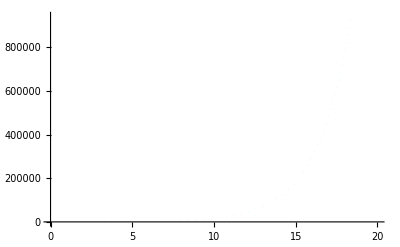

```mathematica
Clear All;
d2 = .137;
v1 =  d2/0.05;
v0   =  0.5* v1;
d0 =  0.1*d2 ; 
d1=  0.5*d2;
p0 = 0.25; 
q0 = 0.2; 
p1 = 0.3; 
q1 = 0.1;

system1 = {
X0'[t] == (p0 - q0)v0 X0[t] - d0 X0[t],
X1'[t] == (1-p0 + q0)v0 X0[t] + (p1 - q1)v1 X1[t] - d1 X1[t] ,
X2'[t] == (1 - p1 + q1)v1 X1[t] - d2 X2[t],
X0[0]==10, X1[0]== 0, X2[0]==0
};


solsym = NDSolve[system1, {X0[t], X1[t], X2[t]}, {t,0,20}];
NoFeed = Plot[Evaluate[{X0[t]+X1[t]+X2[t]}/.solsym],{t,0,20},PlotStyle->{LightGreen, Dotted, Thick}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

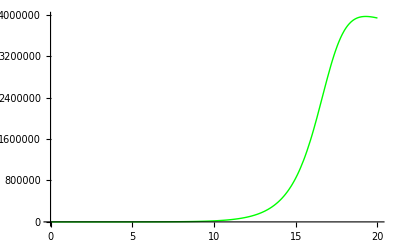

```mathematica
d2 = .1;
v1 =  d2/0.05;
v0   =  0.5* v1;
d0 =  0.1*d2 ; 
d1=  0.5*d2;
p0 = 0.5; 
q0 = 0.2; 
p1 = 0.5; 
q1 = 0.1;
β0 = 2*10^-11;
β1 = 3*10^-12;
τ = 2;

system2 = {
X0'[t] == (p0 - q0)v0/(1+β0*( X2[t-τ])^2) X0[t] - d0 X0[t],
X1'[t] == (1-p0 + q0)v0/(1+β0 *(X2[t-τ])^2) X0[t] + (p1 - q1)v1/(1+β1* (X2[t-τ])^2) X1[t] - d1 *X1[t] ,
X2'[t] == (1 - p1 + q1)v1/(1+β1* (X2[t-τ])^2)X1[t] - d2 X2[t],
X0[0]==3, X1[0]== 0.1, X2[0]==0.1
};

solsym2 = NDSolve[system2, {X0[t], X1[t], X2[t]}, {t,0,20}];
TypeI = Plot[Evaluate[{X0[t]+X1[t]+X2[t]}/.solsym2],{t,0,20},PlotStyle->{Green, Thick}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

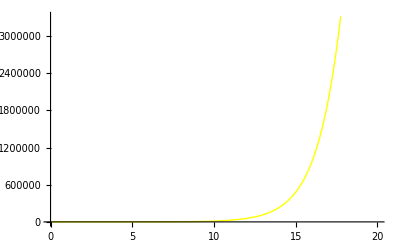

```mathematica
d2 = .095;
v1 =  d2/0.05;
v0   =  0.5* v1;
d0 =  0.1*d2 ; 
d1=  0.5*d2;
p0 = 0.5; 
q0 = 0.2; 
p1 = 0.5; 
q1 = 0.1;
τ = 2;
γ01  = 5*10^-14;
γ02 = 7*10^-15;
γ11 = 6*10^-13;
γ12 = 2*10^-15;

system3 = {
X0'[t] == (p0/(1+γ01*( X2[t-τ])^2) - q0/(1+γ02*( X2[t-τ])^2))v0 *X0[t] - d0 X0[t],
X1'[t] == (1-p0/(1+γ01*( X2[t-τ])^2) + q0/(1+γ02*( X2[t-τ])^2))v0* X0[t] + (p1/(1+γ11*( X2[t-τ])^2)- q1/(1+γ12*( X2[t-τ])^2))v1* X1[t] - d1 *X1[t] ,
X2'[t] == (1 - p1/(1+γ11*( X2[t-τ])^2) +q1/(1+γ12*( X2[t-τ])^2))v1*X1[t] - d2 X2[t],
X0[0]==3, X1[0]== 0, X2[0]==0
};

solsym3 = NDSolve[system3, {X0[t], X1[t], X2[t]}, {t,0,20}];
TypeII = Plot[Evaluate[{X0[t]+X1[t]+X2[t]}/.solsym3],{t,0,20},PlotStyle->{Yellow, Thick}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

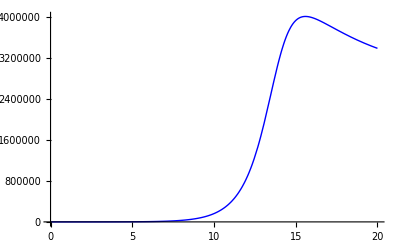

```mathematica
d2 = .112;
v1 =  d2/0.05;
v0   =  0.5* v1;
d0 =  0.1*d2 ; 
d1=  0.5*d2;
p0 = 0.5; 
q0 = 0.2; 
p1 = 0.5; 
q1 = 0.1;
τ = 2;
β0 = 8*10^-11;
β1 = 4*10^-12;
γ01  = 10^-14;
γ02 = 10^-16;
γ11 = 10^-13;
γ12 = 10^-15;

system4 = {
X0'[t] == (p0/(1+γ01*( X2[t-τ])^2) - q0/(1+γ02*( X2[t-τ])^2))*(v0/(1+β0*( X2[t-τ])^2)) *X0[t] - d0 X0[t],
X1'[t] == (1-p0/(1+γ01*( X2[t-τ])^2) + q0/(1+γ02*( X2[t-τ])^2))*(v0/(1+β0*( X2[t-τ])^2))* X0[t] + (p1/(1+γ11*( X2[t-τ])^2)- q1/(1+γ12*( X2[t-τ])^2))*(v1/(1+β1* (X2[t-τ])^2))* X1[t] - d1 *X1[t] ,
X2'[t] == (1 - p1/(1+γ11*( X2[t-τ])^2) +q1/(1+γ12*( X2[t-τ])^2))*(v1/(1+β1* (X2[t-τ])^2))*X1[t] - d2 X2[t],
X0[0]==10, X1[0]== 0, X2[0]==0
};

solsym4 = NDSolve[system4, {X0[t], X1[t], X2[t]}, {t,0,20}];
TypeIandII = Plot[Evaluate[{X0[t]+X1[t]+X2[t]}/.solsym4],{t,0,20},PlotStyle->{Blue, Thick}]
```

```mathematica
Show[NoFeed,TypeI, TypeII, TypeIandII,PlotRange->{0, 4000000} ]
```

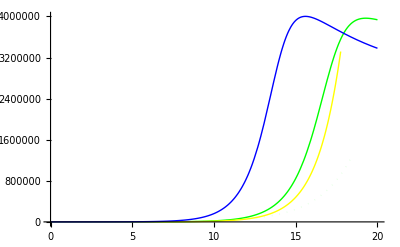
```mathematica
-Graphics- □
```

-Graphics-

Figure 1D

```mathematica
d2 = .084;
v1 =  d2/0.05;
v0   =  0.5* v1;
d0 =  0.1*d2 ; 
d1=  0.5*d2;
p0 = 0.5; 
q0 = 0.2; 
p1 = 0.5; 
q1 = 0.1;
τ = 2;
β0 = 8*10^-27;
β1 = 4*10^-27;
γ01  = 10^-23;
γ02 = 2*10^-24;
γ11 = 4*10^-22;
γ12 = 5*10^-23;

system5 = {
X0'[t] == (p0/(1+γ01*( X2[t-τ])^2) - q0/(1+γ02*( X2[t-τ])^2))*(v0/(1+β0*( X2[t-τ])^2)) *X0[t] - d0 X0[t],
X1'[t] == (1-p0/(1+γ01*( X2[t-τ])^2) + q0/(1+γ01*( X2[t-τ])^2))*(v0/(1+β0*( X2[t-τ])^2))* X0[t] + (p1/(1+γ11*( X2[t-τ])^2)- q1/(1+γ12*( X2[t-τ])^2))*(v1/(1+β1* (X2[t-τ])^2))* X1[t] - d1 *X1[t] ,
X2'[t] == (1 - p1/(1+γ11*( X2[t-τ])^2) +q1/(1+γ12*( X2[t-τ])^2))*(v1/(1+β1* (X2[t-τ])^2))*X1[t] - d2 X2[t],
X0[0]==10, X1[0]== 0, X2[0]==0
};

solsym5 = NDSolve[system5, {X0[t], X1[t], X2[t]}, {t,0,20}];
Fig1D= Plot[Evaluate[{X0[t]+X1[t]+X2[t]}/.solsym5],{t,0,120},PlotStyle->{Blue, Thick}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

-Graphics-

For Problem 1c

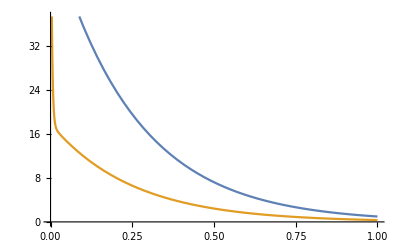

```mathematica
system1c= {
Y1'[t] ==-5*Y1[t] + 3*Y2[t],
Y2'[t] ==  100*Y1[t] - 301*Y2[t],
Y1[0] == 52.29, Y2[0] == 83.82
};

solsym1c =  NDSolve[system1c, {Y1[t], Y2[t]}, {t,0,1}];
Fig1D= Plot[Evaluate[{Y1[t],Y2[t]}/.solsym1c],{t,0,1},PlotStyle->Automatic]
```